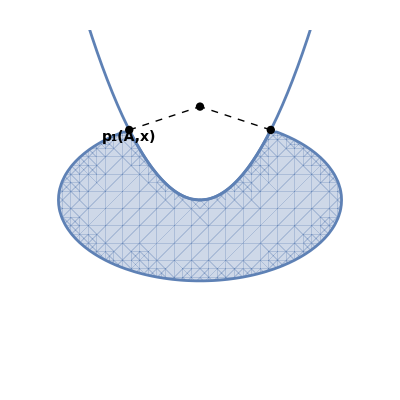

```mathematica
Show[RegionPlot[x^2 + 4y^2 <= 12 && 0.5x^2 >= y, {x, -4, 4}, {y, -3.5, 3.5}, Frame -> False], Plot[0.5x^2, {x, -3, 3}], Graphics[{PointSize[0.015], Point[{0, 2}]}], Graphics[{PointSize[0.015], Point[{{Sqrt[3], 1.5}}], Dashed, Line[{{Sqrt[3], 1.5}, {0, 2}}]}], Graphics[{PointSize[0.015], Point[{-Sqrt[3], 1.5}], Text[Style[, FontSize -> 14, Bold],{-Sqrt[3], 1.2}, Bottom], Dashed, Line[{{-Sqrt[3], 1.5}, {0, 2}}]}]]
```

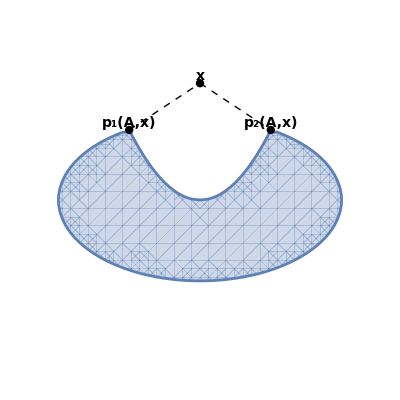

```mathematica
Show[RegionPlot[
  x^2 + 4 y^2 <= 12 && 0.5 x^2 >= y, {x, -4, 4}, {y, -3.5, 3.5}, 
  Frame -> False], 
 Graphics[{PointSize[0.015], Point[{0, 2.5}], Point[{-Sqrt[3], 1.5}], 
   Point[{Sqrt[3], 1.5}]}], 
 Graphics[{Dashed, Line[{{-Sqrt[3], 1.5}, {0, 2.5}}], 
   Line[{{0, 2.5}, {Sqrt[3], 1.5}}]}], 
 Graphics[{Text[Style[Subscript[p, 1](A,x), FontSize -> 14, Bold], {-Sqrt[3], 1.5}, 
    Bottom], Text[Style[x, FontSize -> 14, Bold], {0, 2.5}, Bottom], 
   Text[Style[Subscript[p, 2](A,x), FontSize -> 14, Bold], {Sqrt[3], 1.5}, 
    Bottom]}]]
```